## 1. Исходные данные и их стандартизация

{4436,3}

{1100,5}

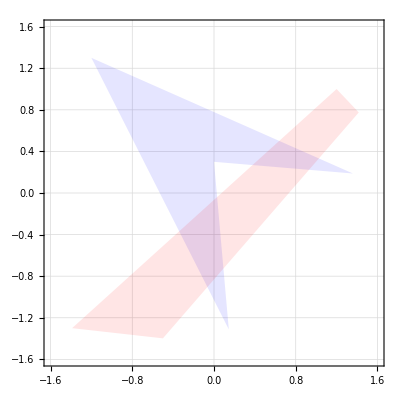

```mathematica
SetDirectory@CurrentValue@"NotebookDirectory";
Dimensions[TrainSet=Import["NG22P09Problem.xlsx",{"Sheets","Train",2;;}]]
Dimensions[TestSet=Import["NG22P09Problem.xlsx",{"Sheets","Test",2;;}]]
Fig0=Uncompress[Import["NG22P09Problem.xlsx",{"Sheets","Fig0"}]⟦1,1⟧]
```

```mathematica
Select[TrainSet, #[[3]]==2&]//Mean
Select[TrainSet, #[[3]]==2&]//StandardDeviation
```

{0.0427433,-0.348666,2.}

{0.662943,0.62937,0.}

```mathematica
Count[TrainSet, Length[#]!=3&]
```

0

```mathematica
TrainSet[[5]][[;;2]]
```

{-1.32691,1.56162}

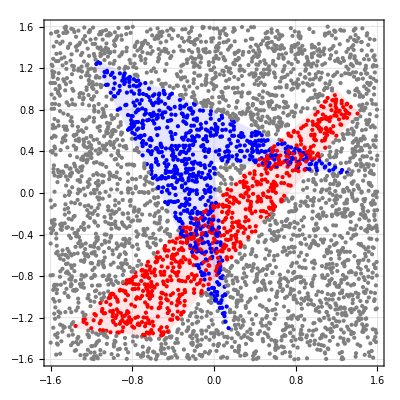

```mathematica
Show[Fig0,Graphics[MapThread[{#1/.{1.->Blue,2.->Red, 3.->Gray},Point[#2]}&,{TrainSet[[All,3]], TrainSet[[All,;;2]]}]]]
```

## 2. Полносвязная нейронная сеть прямого распространения.

```mathematica
ClearAll[LReLU];
```

```mathematica
LReLU = Function[x, If[0 <= x, x, 0.01*x], Listable];
```

```mathematica
LReLU[{{1,2,-3},{1,2,3,-3}}]
```

{{1,2,-0.03},{1,2,3,-0.03}}

```mathematica
DLReLU = LReLU'
```

Function[x,If[0≤x,1,0.01],Listable]

```mathematica
ClearAll[SoftMax]
SoftMax[x_]:=ⅇ^x/Total[ⅇ^x]
```

```mathematica
ClearAll[kmANN];
```

```mathematica
kmANN[]:=Set[kmWeight, Map[RandomReal[0.1*{-1,1},#]&, {{9,3},{12,10},{3,13}}]];
```

```mathematica
kmANN[];
```

```mathematica
Append[TrainSet[[1,;;2]],1]//
kmWeight[[1]].#&//LReLU[#]&//Join[#,{1}]&//kmWeight[[2]].#&//LReLU[#]&//Join[#,{1}]&
```

{-0.00100269,0.0739424,-0.000477044,-0.000807166,0.0458136,-0.000534447,-0.000382504,-0.000534433,0.0552935,0.081778,-0.000442278,0.00860565,1}

```mathematica
kmANN[{x_,y_}]:=Append[{x,y},1]//
kmWeight[[1]].#&//LReLU//Join[#,{1}]&//
kmWeight[[2]].#&//LReLU//Join[#,{1}]&//
kmWeight[[3]].#&//
SoftMax
```

```mathematica
kmANN[{1,1}]
```

{0.325588,0.329177,0.345235}

## 3. Визуализация.

```mathematica
rasterfig = Quiet@Raster[Table[Blend[{Opacity[0.6,Blue],Opacity[0.6,Red], Opacity[0.6,Gray]},kmANN[{x,y}]]/.RGBColor->List, {x,-1.5,1.5,0.1}, {y,-1.5,1.5,0.1}],{{-1.5,-1.5}, {1.5,1.5}}];
```

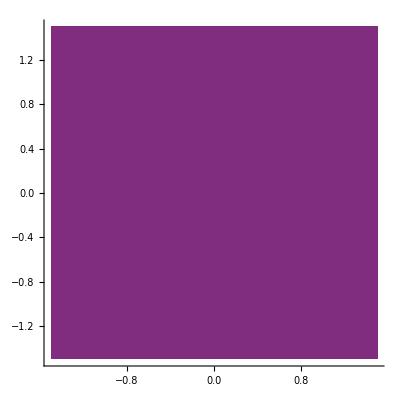

```mathematica
Show[(*Fig0,*)Graphics[rasterfig,Axes->True,PlotRange->{{-1.5,1.5},{-1.5,1.5}}]]
```

## 4. Прямой ход обучения.

```mathematica
ClearAll[kmANN];
```

```mathematica
kmANN[range_]:=Set[kmWeight, Map[RandomReal[range*{-1,1},#]&, {{9,3},{12,10},{3,13}}]];kmANN[{x_,y_}]:=Append[{x,y},1]//Sow[#,yy]&//kmWeight[[1]].#&//Sow[#,vv]&//LReLU//Join[#,{1}]&//Sow[#,yy]&//
kmWeight[[2]].#&//Sow[#,vv]&//LReLU//Append[#,1]&//Sow[#,yy]&//
kmWeight[[3]].#&//Sow[#,vv]&//
SoftMax//Sow[#,yy]&//Chop
```

```mathematica
Reap[kmANN[{1,1}]][[2]][[2]]
```

{{0.0969866,-0.0737452,0.0677911,-0.14808,0.0417075,0.0144652,0.0345846,-0.110408,0.126117},{-0.0914905,0.0785742,-0.0425963,-0.0750237,0.0556622,-0.0360457,-0.0419274,-0.0552265,0.060272,0.08573,-0.0579612,0.00298194},{0.0184801,0.0294415,0.0770741}}

## 5. Локальные градиенты.

```mathematica
kmANN[];
```

```mathematica
ClearAll[findDelta]
findDelta[sample_List]:=Block[{Y= Reap[kmANN[sample[[;;2]]]][[2,1]],V= Reap[kmANN[sample[[;;2]]]][[2,2]],
 wishres = UnitVector[3,Round[sample[[3]]]],delta,l = Length[kmWeight]},delta = {wishres-Last[Y]};
For[i=l,i>1,i--,
PrependTo[delta, DLReLU[V[[i-1]]]*(Most[Transpose[kmWeight[[i]]].First[delta]])]];
Chop@delta]
```

```mathematica
kmWeight[[3]]//Dimensions
```

{3,13}

```mathematica
findDelta[{1,1,1}][[2]]//Dimensions
```

3

{12}

## 6. Обратный ход обучения.

```mathematica
ClearAll[kmΔWeight];
kmΔWeight[sample_List]:=Block[{res,δ = findDelta[sample],Y=Most[Reap[kmANN[sample[[;;2]]]][[2,1]]]},res = Outer[Times,δ[[#]],Y[[#]]]&/@Range[Length[δ]];res]
kmΔWeight[batch:{{_,_,_}..}]:=Sum[kmΔWeight[i],{i,batch}]
```

## 7. Обучение классификатора.

```mathematica
ClearAll[kmTrain];
kmTrain[batch_Integer,η_Real]:=Block[{n=0,batches = Partition[RandomSample[TrainSet],UpTo[batch]],batchCounter},batchCounter=Length[batches];Monitor[Scan[(kmWeight+=η*kmΔWeight[#];n++)&,batches],ProgressIndicator[n,{0,batchCounter}]]];
```

```mathematica
kmTrain[10,0.01]
```

```mathematica
ClearAll[kmEpochTrain];
kmEpochTrain[batch_Integer,η_Real,epoch_Integer]:=Block[{curEpoch=1,cureta=η},Monitor[For[curEpoch=1,curEpoch<=epoch,curEpoch++,kmTrain[batch,cureta];cureta*=0.99;rasterfig =Raster[Table[Blend[{Opacity[0.6,Blue],Opacity[0.6,Red], Opacity[0.6,Gray]},kmANN[{y,x}]]/.RGBColor->List, {x,-1.5,1.5,0.05}, {y,-1.5,1.5,0.05
}],{{-1.5,-1.5}, {1.5,1.5}}]],curEpoch]]
```

```mathematica
kmANN[1];
rasterfig=Raster[Table[Blend[{Opacity[0.6,Blue],Opacity[0.6,Red], Opacity[0.6,Gray]},kmANN[{y,x}]]/.RGBColor->List, {x,-1.5,1.5,0.05}, {y,-1.5,1.5,0.05}],{{-1.5,-1.5}, {1.5,1.5}}];
```

```mathematica
Show[Fig0,Graphics[Dynamic@rasterfig,Axes->True,PlotRange->{{-1.5,1.5},{-1.5,1.5}}]]
```

-Graphics-

```mathematica
kmEpochTrain[10,0.01,100]
```

$Aborted

## 8. Качество обучения.

```mathematica
counter = 0;Scan[If[First[TakeLargest[kmANN[#[[;;2]]]->"Index",1]]==Round[#[[3]]],counter++]&,TrainSet]
counter/Length[TrainSet]//N
```

0.962804

```mathematica
kmWeight = Get["kmWeight.txt"];
rasterfig=Raster[Table[Blend[{Opacity[0.6,Blue],Opacity[0.6,Red], Opacity[0.6,Gray]},kmANN[{y,x}]]/.RGBColor->List, {x,-1.5,1.5,0.05}, {y,-1.5,1.5,0.05}],{{-1.5,-1.5}, {1.5,1.5}}];
 Show[Fig0,Graphics[rasterfig,Axes->True,PlotRange->{{-1.5,1.5},{-1.5,1.5}}]]
```